FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→87089.2,c→235.489,d→0.14345,e→-87072.7}

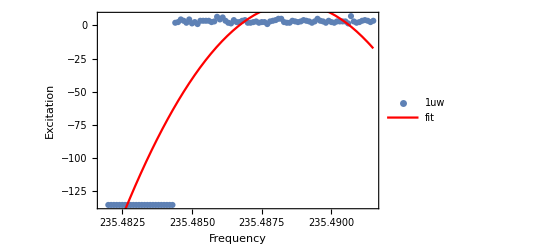

```mathematica
data  =Flatten[Transpose[Import["D:\\Desktop\\435_width\\435_width_iteration_scan_amp=0.045rabi_time=5500fre 235.482-235.494.csv"]]];
n=Length[data]/4;
xdata = data[[1;;n]];
ydata = 100-data[[n+1;;2*n]];
ydata2 = data[[4n+1;;5*n]];
fitdata = Transpose[{xdata, ydata}];
Clear[a,b,c,d,e];
expr = a*Exp[-((x-c)/d)^2]+e;
fitResult = FindFit[fitdata, expr, {{a,27.28},{c,235.491},{d,0.002433},{e,3}},x]
modelFunction  =Function[{x}, Evaluate[expr/.fitResult]];
Show[ListPlot[fitdata,Frame->True,FrameLabel->{"Frequency","Excitation"},PlotLegends->Placed[{"1uw"},{0.1,0.85}]],
Plot[modelFunction[x],{x,Min[xdata],Max[xdata]},PlotStyle->Red,Frame->True,PlotLegends->Placed[{"fit"},{0.1,0.75}]]]
```

```mathematica
2*Sqrt[Log[2]]*d/.fitResult
```

0.00263863

```mathematica
ydata
```

{-135.492,-135.492,-135.492,-135.492,-135.492,-135.492,-135.492,-135.492,-135.492,-135.493,-135.493,-135.493,-135.493,-135.493,-135.493,-135.493,-135.493,-135.493,-135.493,-135.494,-135.494,-135.494,-135.494,-135.494,2.,2.5,4.5,3.5,2.,4.5,1.5,2.5,1.,3.5,3.5,3.5,3.5,2.5,3.,6.5,4.5,6.,3.5,2.,1.5,4.,2.5,2.5,3.5,4.,2.,2.,2.5,3.,2.,2.5,2.5,1.,3.,3.5,4.,5.,5.,2.5,2.,2.,3.5,3.,2.5,3.,4.,3.5,3.,2.,3.,5.,3.5,3.,2.,3.5,2.5,2.,3.,3.,3.,3.,1.5,7.,3.,2.,2.5,3.5,4.,3.5,2.5,3.5}

```mathematica
data[[n+1;;2*n]]
```

{235.492,235.492,235.492,235.492,235.492,235.492,235.492,235.492,235.492,235.493,235.493,235.493,235.493,235.493,235.493,235.493,235.493,235.493,235.493,235.494,235.494,235.494,235.494,235.494,98.,97.5,95.5,96.5,98.,95.5,98.5,97.5,99.,96.5,96.5,96.5,96.5,97.5,97.,93.5,95.5,94.,96.5,98.,98.5,96.,97.5,97.5,96.5,96.,98.,98.,97.5,97.,98.,97.5,97.5,99.,97.,96.5,96.,95.,95.,97.5,98.,98.,96.5,97.,97.5,97.,96.,96.5,97.,98.,97.,95.,96.5,97.,98.,96.5,97.5,98.,97.,97.,97.,97.,98.5,93.,97.,98.,97.5,96.5,96.,96.5,97.5,96.5}